# “Proyecto Final: Mecanismos”

## Ortega Trejo José Eduardo Jaimes Arriaga Donovan Zuriel Dr. José Antonio Silva Rico 2020-2

## Solución cinemática

## Datos

```mathematica
θ0 = 190*Degree;
θ2 = 60*Degree;
r0=1.3* 0.1;
r1=0.08* 0.1;
r2= 0.08* 0.1;       (*valores de r2 [0,0.23765]*)
r3=1.25* 0.1;
r4=0.7* 0.1;
r5=0.4* 0.1;
r5p= 0.4* 0.1;
r6=1.15* 0.1;
```

## Ecuaciones Cinemáticas

```mathematica
Clear[θ2,θ3,θ4,θ5,θ6];
Clear[ω2,ω3,ω4,ω5,ω6];
Clear[α2,α3,α4,α5,α6];
```

### Ecuaciones de Posición

```mathematica
u0 ={Cos[θ0],Sin[θ0],0};
u1 = {Cos[θ2+Pi],Sin[θ2+Pi], 0};
u2 = {Cos[θ2 ], Sin[θ2],0};
u3 = {Cos[θ3], Sin[θ3],0};
u4 = {Cos[θ4], Sin[θ4],0};
u5={Cos[θ5], Sin[θ5],0};
u6 = {Cos[θ6], Sin[θ6],0};

R0 = r0 * u0;
R1 = r1 * u1;
R2 = r2*u2;
R3=r3 * u3;
R4 = r4 *u4;          
R5= r5* u5;
R5p = r5p* u5;
R6 = r6 * u6;


(*Lazos vectoriales*)
pos1 = R2 +R3-R5 - R0;
pos2 = R1+ R4 + R6 - R5p -R3 -R2;

pos1 // MatrixForm
pos2 // MatrixForm
```

(0.128025+0.008 Cos[θ2]+0.125 Cos[θ3]-0.04 Cos[θ5]
0.0225743+0.008 Sin[θ2]+0.125 Sin[θ3]-0.04 Sin[θ5]
0.)

(-0.016 Cos[θ2]-0.125 Cos[θ3]+0.07 Cos[θ4]-0.04 Cos[θ5]+0.115 Cos[θ6]
-0.016 Sin[θ2]-0.125 Sin[θ3]+0.07 Sin[θ4]-0.04 Sin[θ5]+0.115 Sin[θ6]
0.)

### Ecuaciones de Velocidad

```mathematica
omega2 = {0,0,ω2};
omega3= {0,0,ω3};
omega4 = {0,0,ω4};
omega5= {0,0,ω5};
omega6= {0,0,ω6};

V0 = {0,0,0};
V1 = omega2 ×R1;
V2 = omega2×R2;
V3 = omega3 × R3;
V4 = omega4 ×R4;
V5 = omega5 ×R5;
V5p = omega5 ×R5p;
V6 = omega6 ×R6;

(*Lazos vectoriales*)
vel1 =V2 +V3-V5 - V0;
vel2= V1+ V4 + V6 - V5p -V3 -V2;

vel1 // MatrixForm
vel2//  MatrixForm
```

(0.-0.008 ω2 Sin[θ2]-0.125 ω3 Sin[θ3]+0.04 ω5 Sin[θ5]
0.+0.008 ω2 Cos[θ2]+0.125 ω3 Cos[θ3]-0.04 ω5 Cos[θ5]
0.)

(0.+0.016 ω2 Sin[θ2]+0.125 ω3 Sin[θ3]-0.07 ω4 Sin[θ4]+0.04 ω5 Sin[θ5]-0.115 ω6 Sin[θ6]
0.-0.016 ω2 Cos[θ2]-0.125 ω3 Cos[θ3]+0.07 ω4 Cos[θ4]-0.04 ω5 Cos[θ5]+0.115 ω6 Cos[θ6]
0.)

### Ecuaciones de Aceleración

```mathematica
alfa2 = {0,0,α2};
alfa3 = {0,0,α3};
alfa4 = {0,0,α4};
alfa5 = {0,0,α5};
alfa6= {0,0,α6};

A0 = {0,0,0};
A1 = alfa2×R1 + ω2^2 * R1;
A2 = alfa2×R2 + ω2^2 * R2;
A3 = alfa3×R3 + ω3^2 * R3;
A4 = alfa4×R4 + ω4^2 * R4;
A5= alfa5×R5 + ω5^2 * R5;
A5p = alfa5×R5p+ ω5^2 * R5p;
A6= alfa6×R6 + ω6^2 * R6;

(*Lazos vectoriales*)
acel1 = A2 +A3-A5 - A0;
acel2 = A1+ A4 + A6 - A5p -A3 -A2;

acel1// MatrixForm
acel2 // MatrixForm
```

(0.+0.008 ω2^2 Cos[θ2]+0.125 ω3^2 Cos[θ3]-0.04 ω5^2 Cos[θ5]-0.008 α2 Sin[θ2]-0.125 α3 Sin[θ3]+0.04 α5 Sin[θ5]
0.+0.008 α2 Cos[θ2]+0.125 α3 Cos[θ3]-0.04 α5 Cos[θ5]+0.008 ω2^2 Sin[θ2]+0.125 ω3^2 Sin[θ3]-0.04 ω5^2 Sin[θ5]
0.)

(0.-0.016 ω2^2 Cos[θ2]-0.125 ω3^2 Cos[θ3]+0.07 ω4^2 Cos[θ4]-0.04 ω5^2 Cos[θ5]+0.115 ω6^2 Cos[θ6]+0.016 α2 Sin[θ2]+0.125 α3 Sin[θ3]-0.07 α4 Sin[θ4]+0.04 α5 Sin[θ5]-0.115 α6 Sin[θ6]
0.-0.016 α2 Cos[θ2]-0.125 α3 Cos[θ3]+0.07 α4 Cos[θ4]-0.04 α5 Cos[θ5]+0.115 α6 Cos[θ6]-0.016 ω2^2 Sin[θ2]-0.125 ω3^2 Sin[θ3]+0.07 ω4^2 Sin[θ4]-0.04 ω5^2 Sin[θ5]+0.115 ω6^2 Sin[θ6]
0.)

## Solución Posición

```mathematica
Clear[θ2,θ3,θ4,θ5,θ6];

θ2 = 60 * Degree;(*Variable de control, ángulo de posisción inicial*)
SolInicial=FindRoot[{
pos1⟦1⟧==0,
pos1⟦2⟧==0,
pos2⟦1⟧==0,
pos2⟦2⟧==0},

{{θ3,170*Degree},
{θ4,80*Degree},
{θ5,80*Degree},
{θ6,180*Degree}},
MaxIterations->30]

(θ3/.SolInicial)/Degree
(θ4/.SolInicial)/Degree
(θ5/.SolInicial)/Degree
(θ6/.SolInicial)/Degree
```

{θ3→3.06307,θ4→1.4908,θ5→1.38447,θ6→3.20082}

175.501

85.4166

79.324

183.393

## Solución total

```mathematica
Clear[θ2,θ3,θ4,θ5,θ6];

θ3i=θ3/.SolInicial;
θ4i=θ4/.SolInicial;
θ5i=θ5/.SolInicial;
θ6i=θ6/.SolInicial;


For[i=60,i≤420,i+=1,
θ2=i*Degree;
SolPos[i]=FindRoot[{
pos1⟦1⟧==0,
pos1⟦2⟧==0,
pos2⟦1⟧==0,
pos2⟦2⟧==0},
{{θ3,θ3i},
{θ4,θ4i},
{θ5,θ5i},
{θ6,θ6i}},
MaxIterations->300];
θ3i=θ3/.SolPos[i];
θ4i=θ4/.SolPos[i];
θ5i=θ5/.SolPos[i];
θ6i=θ6/.SolPos[i];];
```

## Gráficas de Posición

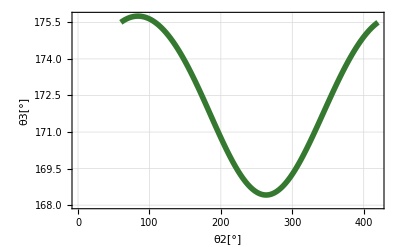

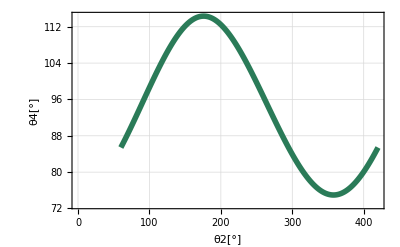

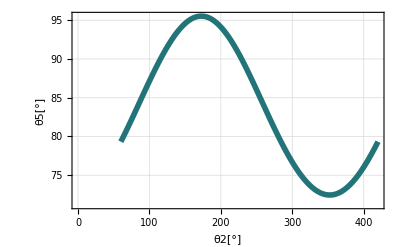

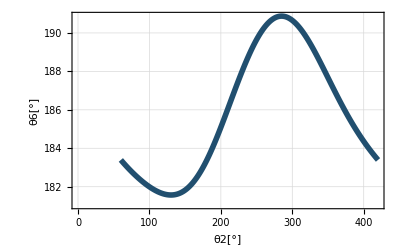

```mathematica
tabla1=Table[{i,(θ3/.SolPos[i])/Degree},{i,60,420,1}];
tabla2=Table[{i,(θ4/.SolPos[i])/Degree},{i,60,420,1}];
tabla3=Table[{i,(θ5/.SolPos[i])/Degree},{i,60,420,1}];
tabla4=Table[{i,(θ6/.SolPos[i])/Degree},{i,60,420,1}];



ListPlot[tabla1,
Frame->True,
FrameLabel->{"θ2[°]","θ3[°]"},
Joined->True,
PlotStyle->{RGBColor[0.2078,0.4745,0.1882],Thickness[.01]},
GridLines->Automatic,
ImageSize->400]

ListPlot[tabla2,
Frame->True,
FrameLabel->{"θ2[°]","θ4[°]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{RGBColor[0.1647,0.4823,0.345],Thickness[.01]},
ImageSize->400]


ListPlot[tabla3,
Frame->True,
FrameLabel->{"θ2[°]","θ5[°]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{RGBColor[0.1372,0.4549,0.4705],Thickness[.01]},
ImageSize->400]

ListPlot[tabla4,
Frame->True,
FrameLabel->{"θ2[°]","θ6[°]"},
Joined->True,
GridLines->Automatic,
PlotStyle->{RGBColor[0.1294,0.3098,0.4352],Thickness[.01]},
ImageSize->400]
```

## Solución Velocidad

```mathematica
Clear[θ2,θ3,θ4,θ5,θ6];
Clear[ω2,ω3,ω4,ω5,ω6];

ω2=50;
For[i=60,i≤420,i+=1,
θ2=i*Degree;
SolVel[i]=Solve[{        
vel1[[1]]==0,
vel1[[2]]==0,
vel2[[1]]==0,
vel2[[2]]==0}/.SolPos[i],      
{ω3,ω4,ω5,ω6}]//Flatten ]
?SolVel;
```

## Gráficas Velocidad

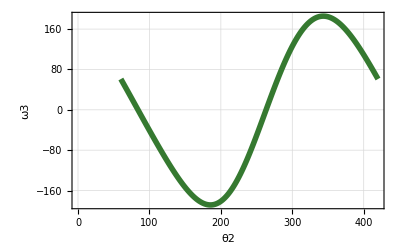

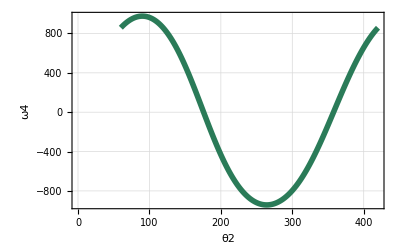

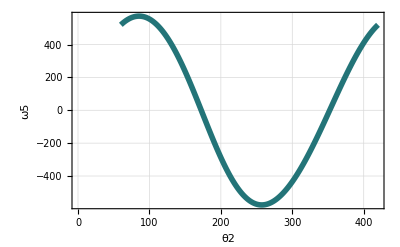

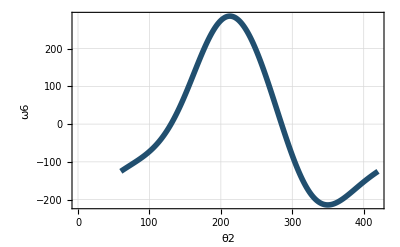

```mathematica
tabla1=Table[{i,(ω3/.SolVel[i])/Degree},{i,60,420,1}];
tabla2=Table[{i,(ω4/.SolVel[i])/Degree},{i,60,420,1}];
tabla3=Table[{i,(ω5/.SolVel[i])/Degree},{i,60,420,1}];
tabla4=Table[{i,(ω6/.SolVel[i])/Degree},{i,60,420,1}];


ListPlot[tabla1,
Frame->True,
FrameLabel->{"θ2","ω3"},
Joined->True,
PlotStyle->{RGBColor[0.2078,0.4745,0.1882],Thickness[.01]},
GridLines->Automatic,
ImageSize->400]

ListPlot[tabla2,
Frame->True,
FrameLabel->{"θ2","ω4"},
Joined->True,
PlotStyle->{RGBColor[0.1647,0.4823,0.345],Thickness[.01]},
GridLines->Automatic,
ImageSize->400]

ListPlot[tabla3,
Frame->True,
FrameLabel->{"θ2","ω5"},
Joined->True,
PlotStyle->{RGBColor[0.1372,0.4549,0.4705],Thickness[.01]},
GridLines->Automatic,
ImageSize->400]

ListPlot[tabla4,
Frame->True,
FrameLabel->{"θ2","ω6"},
Joined->True,
PlotStyle->{RGBColor[0.1294,0.3098,0.4352],Thickness[.01]},
GridLines->Automatic,
ImageSize->400]
```

## Solución aceleración

```mathematica
Clear[θ2,θ3,θ4,θ5,θ6];
Clear[ω2,ω3,ω4,ω5,ω6];
Clear[α2,α3,α4,α5,α6];

ω2=50;
α2=0;
For[i=60,i≤420,i+=1,
θ2=i*Degree;
SolAcel[i]=Solve[{        
acel1[[1]]==0,
acel1[[2]]==0,
acel2[[1]]==0,
acel2[[2]]==0}/.SolPos[i]/.SolVel[i],      
{α3,α4,α5,α6}]//Flatten ]
?SolAcel;
```

## Gráficas de Aceleración

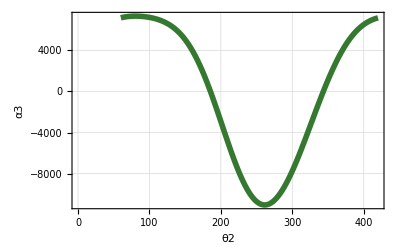

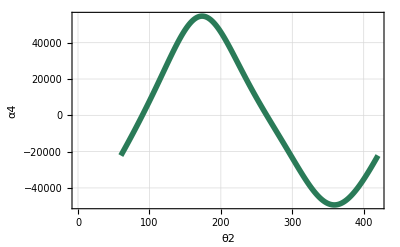

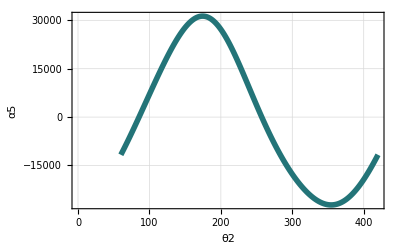

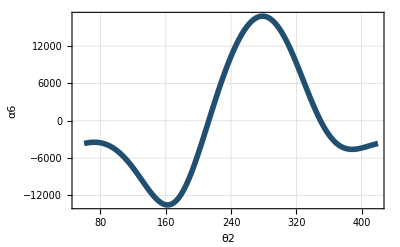

```mathematica
tabla1=Table[{i,(α3/.SolAcel[i])/Degree},{i,60,420,1}];
tabla2=Table[{i,(α4/.SolAcel[i])/Degree},{i,60,420,1}];
tabla3=Table[{i,(α5/.SolAcel[i])/Degree},{i,60,420,1}];
tabla4=Table[{i,(α6/.SolAcel[i])/Degree},{i,60,420,1}];


ListPlot[tabla1,
Frame->True,
FrameLabel->{"θ2","α3"},
Joined->True,
PlotStyle->{RGBColor[0.2078,0.4745,0.1882],Thickness[.01]},
GridLines->Automatic,
ImageSize->400]

ListPlot[tabla2,
Frame->True,
FrameLabel->{"θ2","α4"},
Joined->True,
PlotStyle->{RGBColor[0.1647,0.4823,0.345],Thickness[.01]},
GridLines->Automatic,
ImageSize->400]

ListPlot[tabla3,
Frame->True,
FrameLabel->{"θ2","α5"},
Joined->True,
PlotStyle->{RGBColor[0.1372,0.4549,0.4705],Thickness[.01]},
GridLines->Automatic,
ImageSize->400]

ListPlot[tabla4,
Frame->True,
FrameLabel->{"θ2","α6"},
PlotRange->Full,
Joined->True,
PlotStyle->{RGBColor[0.1294,0.3098,0.4352],Thickness[.01]},
GridLines->Automatic,
ImageSize->400]
```

## Simulación

```mathematica
Clear[θ2,θ3,θ4,θ5,θ6];
Animate[
θ2=i*Degree;
cero={0,0,0};
k={0,0,1};
diametro=0.002;
diametro2=0.002;


eslabon0=Cylinder[{cero,R0},diametro]/.SolPos[i];
eslabon5=Cylinder[{R0+0.004*k,R0+R5+0.004*k},diametro]/.SolPos[i];
eslabon5p=Cylinder[{R0+R5+0.004*k,R0+R5+R5p+0.004*k},diametro]/.SolPos[i];
eslabon2=Cylinder[{cero+0.012*k,R2+0.012*k},diametro]/.SolPos[i];
eslabon3=Cylinder[{R2+0.016*k,R2+R3+0.016*k},diametro]/.SolPos[i];
eslabon1=Cylinder[{cero+0.008*k,R1+0.008*k},diametro]/.SolPos[i];
circuloeslabon1=Cylinder[{R1+0.01*k,R1+0.006*k},0.012]/.SolPos[i];
eslabon4=Cylinder[{R1+0.004*k,R1+R4+0.004*k},diametro]/.SolPos[i];
circuloeslabon4=Cylinder[{R1+0.006*k,R1+0.002*k},0.014]/.SolPos[i];
eslabon6=Cylinder[{R1+R4+0.008*k,R1+R4+R6+0.008*k},diametro]/.SolPos[i];


ejeA=Cylinder[{cero+0.014*k,cero-0.004*k},diametro2]/.SolPos[i];
ejeB=Cylinder[{R2+0.02*k,R2+0.01*k},diametro2]/.SolPos[i];
ejeD=Cylinder[{R0+0.008*k,R0-0.004*k},diametro2]/.SolPos[i];
ejeE=Cylinder[{R2+R3+0.02*k,R2+R3-0*k},diametro2]/.SolPos[i];
ejeF=Cylinder[{R1+R4+R6+0.012*k,R1+R4+R6-0*k},diametro2]/.SolPos[i];
ejeG=Cylinder[{R1+R4+0.012*k,R1+R4-0*k},diametro2]/.SolPos[i];


barra0=Graphics3D[{RGBColor[0.2078,0.4745,0.1882],eslabon0}];
barra5=Graphics3D[{RGBColor[0.1372, 0.4549, 0.4705],eslabon5}];
barra5p=Graphics3D[{RGBColor[0.1372, 0.4549, 0.4705],eslabon5p}];
barra2=Graphics3D[{RGBColor[0.1292, 0.3098, 0.4352],eslabon2}];
barra3=Graphics3D[{RGBColor[0.1529, 0.1294, 0.4274],eslabon3}];
barra1=Graphics3D[{RGBColor[0.1292, 0.3098, 0.4352],eslabon1}];
circulobarra1=Graphics3D[{RGBColor[0.1292, 0.3098, 0.4352],circuloeslabon1}];
barra4=Graphics3D[{RGBColor[0.2784, 0.1293, 0.4294],eslabon4}];
circulobarra4=Graphics3D[{RGBColor[0.2784, 0.1293, 0.4294],circuloeslabon4}];
barra6=Graphics3D[{RGBColor[0.1647, 0.4823, 0.345],eslabon6}];


pernoA=Graphics3D[{GrayLevel[0],ejeA}];
pernoB=Graphics3D[{GrayLevel[0],ejeB}];
pernoD=Graphics3D[{GrayLevel[0],ejeD}];
pernoE=Graphics3D[{GrayLevel[0],ejeE}];
pernoF=Graphics3D[{GrayLevel[0],ejeF}];
pernoG=Graphics3D[{GrayLevel[0],ejeG}];



Show[barra0,barra5,barra5p,barra2,barra3,barra1,circulobarra1,barra4,circulobarra4,barra6,pernoA,pernoB,pernoD,pernoE,pernoF,pernoG,(*La función Show permiter enlistar los elementos que se desean mostrar así como las propiedades del gráfico*)
Axes->True,       
AxesLabel->{"x","y","z"},  
ImageSize->800, 
ViewPoint->{0,1,2},    (*Esta función se emplea para definir el punto desde donde se visualizará la animación, teniendo como referencia el eje de coordenadas que se estableción en la animación*)
ViewVertical->{0,1,0},    (*Esta función permite definir el eje que estará de manera vertical en la animación*)
PlotRange->{{-0.2,0.1},{-0.1, 0.1},{-0.05,0.05}}],    
{i,60,420,1}
]
```

# Solución Dinámica

## Datos y Cinemática de centros de masa

## Datos

```mathematica
aKG = 0.001;                    (*kg*)
m12 = 27.72*aKG;
m3 = 14.33*aKG;
m4 = 14.02*aKG;
m5 = 18.24*aKG;
m6 = 19.17*aKG;


ψ1=2.8*Degree;
ψp=30*Degree;

d12=0.00175;                  (*m*)
d3=0.0625;
d4=0.03363;
d5=0.03775;
d6=0.02944;
dp=0.005;

InertiaConv = 0.000000001;
Ig12 = 8061.84 *InertiaConv;              (*kg.m^2*)
Ig3 = 25654.01 *InertiaConv;
Ig4 = 10118.87*InertiaConv;
Ig5 = 13175.67 * InertiaConv;
Ig6 = 72531.46 * InertiaConv;
```

## Posición centros de masa

```mathematica
Clear[θ2,θ3,θ4,θ5,θ6];
Clear[ω2,ω3,ω4,ω5,ω6];
Clear[α2,α3,α4,α5,α6];
```

```mathematica
Rg3p=d3*u3;
Rg4p=d4*u4;
Rg5p=d5*u5;
Rg6p=d6*{Cos[θ6-ψ1],Sin[θ6-ψ1],0};
Rpp=dp*{Cos[θ6-ψp],Sin[θ6-ψp],0};


Rg12=d12*u2;
Rg3=R2+Rg3p;
Rg4=R1+Rg4p;
Rg5=R0+Rg5p;
Rg6=R1+R4+Rg6p;
Rp=R1+R4+Rg6p+Rpp;
```

## Velocidad de centros de masa

```mathematica
Clear[θ2,θ3,θ4,θ5,θ6];
Clear[ω2,ω3,ω4,ω5,ω6];
Clear[α2,α3,α4,α5,α6];
```

```mathematica
Vg3p=omega3×Rg3p;
Vg4p=omega4×Rg4p;
Vg5p=omega5×Rg5p;
Vg6p=omega6×Rg6p;
Vpp=omega6×Rpp;



Vg12=omega2×Rg12;
Vg3=V2+Vg3p;
Vg4=V1+Vg4p;
Vg5=V0+Vg5p;
Vg6=V1+ V4+Vg6p;
Vp=V1+V4+Vg6p+Vpp;
```

## Aceleración de centros de masa

```mathematica
Clear[θ2,θ3,θ4,θ5,θ6];
Clear[ω2,ω3,ω4,ω5,ω6];
Clear[α2,α3,α4,α5,α6];
```

```mathematica
Ag3p=alfa3×Rg3p-ω3^2*Rg3p;
Ag4p=alfa4×Rg4p-ω4^2*Rg4p;
Ag5p=alfa5×Rg5p-ω5^2*Rg5p;
Ag6p=alfa6×Rg6p-ω6^2*Rg6p;


Ag12=alfa2×Rg12-ω2^2*Rg12;
Ag3=A2+Ag3p;
Ag4=A1+Ag4p;
Ag5=A0+Ag5p;
Ag6=A1+A4+Ag6p;
```

## Vectores de brazos de palanca

```mathematica
Clear[θ2,θ3,θ4,θ5,θ6];
Clear[ω2,ω3,ω4,ω5,ω6];
Clear[α2,α3,α4,α5,α6];


R01 = -Rg12;
R41 = (r1+d12)*u1;
R32  = (r2- d12)*u2;
R14 = -Rg4p;
R64 = (r4 - d4)*u4;
R23 = -Rg3p;
R53 = (r3 - d3)*u3;
R05 = -Rg5p;
R35 = (r5 - d5)*u5;
R65 = (r5 + r5p - d5)* u5;
R56 = -Rg6p + r6*u6;
R46 = -Rg6p;
```

## Dinámica Newton con Peso

## Ecuaciones Dinámicas

```mathematica
Clear[θ2,θ3,θ4,θ5,θ6];
Clear[ω2,ω3,ω4,ω5,ω6];
Clear[α2,α3,α4,α5,α6];
```

```mathematica
g=9.81;(*m/s^2*)


F41 = {f41x,f41y,0};
F32 = {f32x,f32y,0};
F53 = {f53x,f53y,0};
F46 = {f46x,f46y,0};
F56 = {f56x, f56y,0};
F01 = {f01x,f01y,0};
F05 = {f05x,f05y,0};

Fp=5*{Cos[270*Degree],Sin[270*Degree],0};

T01={0,0,t01z};

T05=-{0,0,ω5};


W12 ={0,m12*g,0};
W3 ={0,m3*g,0};
W4 ={0,m4*g,0};
W5 ={0,m5*g,0};
W6 ={0,m6*g ,0};




(*Cuerpo 12*)
EcNew1 = -F41+ F01-F32 - W12 -m12*Ag12;
EcEul1 = T01+R41×(-F41)+R01×F01+R32×(-F32)-Ig12*alfa2;


(*Cuerpo 3*)
EcNew3 = -F53+F32-W3 - m3*Ag3;
EcEul3 = R53×(-F53)+R23×F32-Ig3*alfa3;

(*Cuerpo 4*)
EcNew4 = F46 + F41 -W4 -m4*Ag4;
EcEul4 = R64×F46+R14×F41-Ig4*alfa4;

(*Cuerpo 5*)
EcNew5 = F56 + F53 + F05 - W5 - m5*Ag5;
EcEul5 = T05 +R65×F56+R35×F53+ R05×F05-Ig5*alfa5;

(*Cuerpo 6*)
EcNew6 = Fp-F56-F46-W6 - m6*Ag6;
EcEul6 = Rpp×Fp+ R56×(-F56)+R46×(-F46)-Ig6*alfa6;
```

## Solución Dinámica

```mathematica
Clear[θ2,θ3,θ4,θ5,θ6];
Clear[ω2,ω3,ω4,ω5,ω6];
Clear[α2,α3,α4,α5,α6];

α2=0;
ω2=50;
For[i=60,i≤420,i+=1,
θ2=i*Degree;
SolDin[i]=Solve[{
EcNew1⟦1⟧==0,
EcNew1⟦2⟧==0,
EcEul1⟦3⟧==0,
EcNew3⟦1⟧==0,
EcNew3⟦2⟧==0,
EcEul3⟦3⟧==0,
EcNew4⟦1⟧==0,
EcNew4⟦2⟧==0,
EcEul4⟦3⟧==0,
EcNew5⟦1⟧==0,
EcNew5⟦2⟧==0,
EcEul5⟦3⟧==0,
EcNew6⟦1⟧==0,
EcNew6⟦2⟧==0,
EcEul6⟦3⟧==0}/.SolPos[i]/.SolVel[i]/.SolAcel[i],
{f41x,f41y,f32x,f32y,f53x,f53y,f46x,f46y,f56x,f56y,f01x,f01y,f05x,f05y,t01z}]//Flatten;]
??SolDin;
```

Missing[UnknownSymbol,SolDin;]

## Gráficas de Reacciones

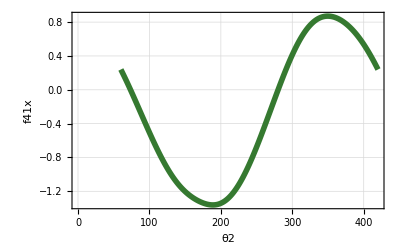

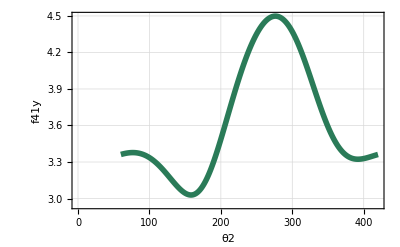

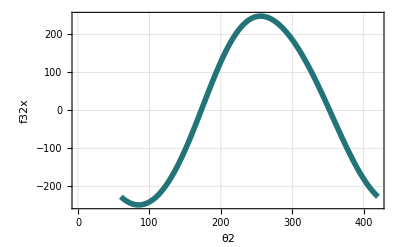

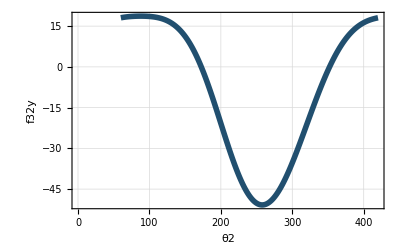

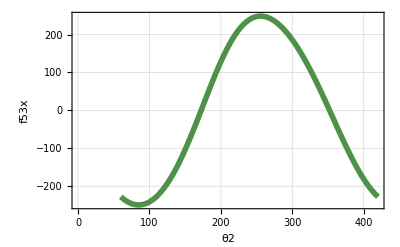

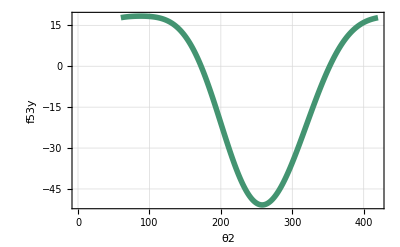

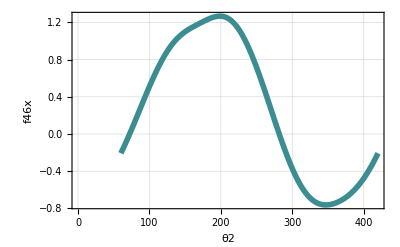

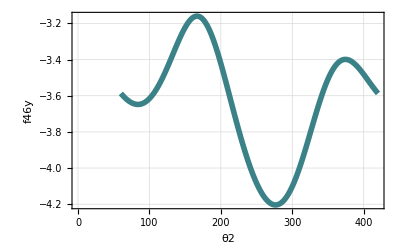

```mathematica
tablaA=Table[{i,f41x}/.SolDin[i],{i,60,420,1}];
tablaB=Table[{i,f41y}/.SolDin[i],{i,60,420,1}];
tablaC=Table[{i,f32x}/.SolDin[i],{i,60,420,1}];
tablaD=Table[{i,f32y}/.SolDin[i],{i,60,420,1}];
tablaE=Table[{i,f53x}/.SolDin[i],{i,60,420,1}];
tablaF=Table[{i,f53y}/.SolDin[i],{i,60,420,1}];
tablaG=Table[{i,f46x}/.SolDin[i],{i,60,420,1}];
tablaH=Table[{i,f46y}/.SolDin[i],{i,60,420,1}];
tablaI=Table[{i,f56x}/.SolDin[i],{i,60,420,1}];
tablaJ=Table[{i,f56y}/.SolDin[i],{i,60,420,1}];
tablaK=Table[{i,f01x}/.SolDin[i],{i,60,420,1}];
tablaL=Table[{i,f01y}/.SolDin[i],{i,60,420,1}];
tablaM=Table[{i,f05x}/.SolDin[i],{i,60,420,1}];
tablaN=Table[{i,f05y}/.SolDin[i],{i,60,420,1}];
tablaO=Table[{i,t01z}/.SolDin[i],{i,60,420,1}];
ListPlot[tablaA,  Frame->True,  FrameLabel->{"θ2","f41x"},   Joined->True,      PlotStyle->{RGBColor[0.2078,0.4745,0.1882],Thickness[.01]},    GridLines->Automatic,    ImageSize->400]

ListPlot[tablaB,  Frame->True,  FrameLabel->{"θ2","f41y"},  Joined->True,  PlotStyle->{RGBColor[0.1647,0.4823,0.345],Thickness[.01]},  GridLines->Automatic,  ImageSize->400]

ListPlot[tablaC,  Frame->True,  FrameLabel->{"θ2","f32x"},  Joined->True,  PlotStyle->{RGBColor[0.1372,0.4549,0.4705],Thickness[.01]},  GridLines->Automatic,  ImageSize->400]

ListPlot[tablaD,  Frame->True,  FrameLabel->{"θ2","f32y"},  Joined->True,  PlotStyle->{RGBColor[0.1294,0.3098,0.4352],Thickness[.01]},  GridLines->Automatic,  ImageSize->400]

ListPlot[tablaE,  Frame->True,  FrameLabel->{"θ2","f53x"},   Joined->True,      PlotStyle->{RGBColor[0.3078,0.5745,0.2882],Thickness[.01]},    GridLines->Automatic,    ImageSize->400]

ListPlot[tablaF,  Frame->True,  FrameLabel->{"θ2","f53y"},  Joined->True,  PlotStyle->{RGBColor[0.2647,0.5823,0.445],Thickness[.01]},  GridLines->Automatic,  ImageSize->400]

ListPlot[tablaG,  Frame->True,  FrameLabel->{"θ2","f46x"},  Joined->True,  PlotStyle->{RGBColor[0.2372,0.5549,0.5705],Thickness[.01]},  GridLines->Automatic,  ImageSize->400]

ListPlot[tablaH,  Frame->True,  FrameLabel->{"θ2","f46y"},  Joined->True,  PlotStyle->{RGBColor[0.2294,0.5098,0.5352],Thickness[.01]},  GridLines->Automatic,  ImageSize->400]
ListPlot[tablaI,  Frame->True,  FrameLabel->{"θ2","f56x"},   Joined->True,      PlotStyle->{RGBColor[0.4078,0.6745,0.3882],Thickness[.01]},    GridLines->Automatic,    ImageSize->400]

ListPlot[tablaJ,  Frame->True,  FrameLabel->{"θ2","f56y"},  Joined->True,  PlotStyle->{RGBColor[0.3647,0.6823,0.545],Thickness[.01]},  GridLines->Automatic,  ImageSize->400]

ListPlot[tablaK,  Frame->True,  FrameLabel->{"θ2","f01x"},  Joined->True,  PlotStyle->{RGBColor[0.3372,0.6549,0.6705],Thickness[.01]},  GridLines->Automatic,  ImageSize->400]

ListPlot[tablaL,  Frame->True,  FrameLabel->{"θ2","f01y"},  Joined->True,  PlotStyle->{RGBColor[0.3294,0.5098,0.6352],Thickness[.01]},  GridLines->Automatic,  ImageSize->400]
ListPlot[tablaM,  Frame->True,  FrameLabel->{"θ2","f05x"},   Joined->True,      PlotStyle->{RGBColor[0.5078,0.7745,0.4882],Thickness[.01]},    GridLines->Automatic,    ImageSize->400]

ListPlot[tablaN,  Frame->True,  FrameLabel->{"θ2","f05y"},  Joined->True,  PlotStyle->{RGBColor[0.4647,0.7823,0.645],Thickness[.01]},  GridLines->Automatic,  ImageSize->400]

ListPlot[tablaO,  Frame->True,  FrameLabel->{"θ2","t01z"},  Joined->True,  PlotStyle->{RGBColor[0.4372,0.7549,0.7705],Thickness[.01]},  GridLines->Automatic,  ImageSize->400]
```

### Gráficas de Normas de las fuerzas de reacción

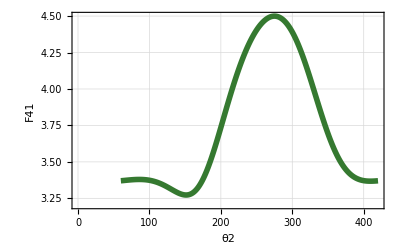

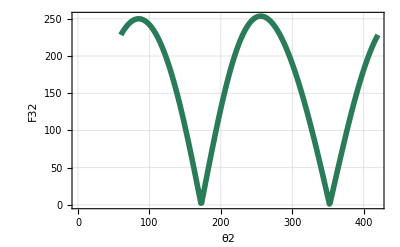

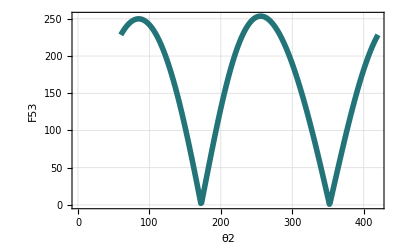

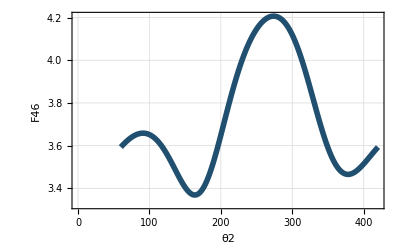

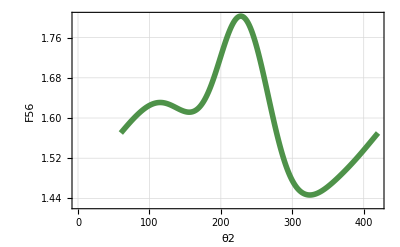

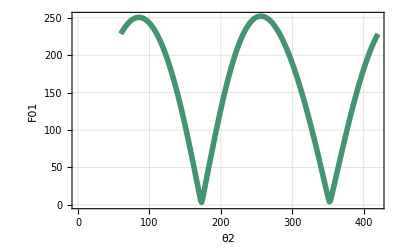

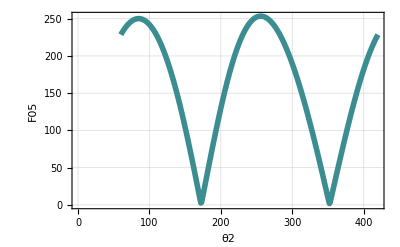

```mathematica
tablaP=Table[{i,Norm[F41]}/.SolDin[i],{i,60,420,1}];
tablaQ=Table[{i,Norm[F32]}/.SolDin[i],{i,60,420,1}];
tablaR=Table[{i,Norm[F53]}/.SolDin[i],{i,60,420,1}];
tablaS=Table[{i,Norm[F46]}/.SolDin[i],{i,60,420,1}];
tablaT=Table[{i,Norm[F56]}/.SolDin[i],{i,60,420,1}];
tablaU=Table[{i,Norm[F01]}/.SolDin[i],{i,60,420,1}];
tablaV=Table[{i,Norm[F05]}/.SolDin[i],{i,60,420,1}];

ListPlot[tablaP,  Frame->True,  FrameLabel->{"θ2","F41"},   Joined->True,      PlotStyle->{RGBColor[0.2078,0.4745,0.1882],Thickness[.01]},    GridLines->Automatic,    ImageSize->400]

ListPlot[tablaQ,  Frame->True,  FrameLabel->{"θ2","F32"},  Joined->True,  PlotStyle->{RGBColor[0.1647,0.4823,0.345],Thickness[.01]},  GridLines->Automatic,  ImageSize->400]

ListPlot[tablaR,  Frame->True,  FrameLabel->{"θ2","F53"},  Joined->True,  PlotStyle->{RGBColor[0.1372,0.4549,0.4705],Thickness[.01]},  GridLines->Automatic,  ImageSize->400]

ListPlot[tablaS,  Frame->True,  FrameLabel->{"θ2","F46"},  Joined->True,  PlotStyle->{RGBColor[0.1294,0.3098,0.4352],Thickness[.01]},  GridLines->Automatic,  ImageSize->400]

ListPlot[tablaT,  Frame->True,  FrameLabel->{"θ2","F56"},   Joined->True,      PlotStyle->{RGBColor[0.3078,0.5745,0.2882],Thickness[.01]},    GridLines->Automatic,    ImageSize->400]

ListPlot[tablaU,  Frame->True,  FrameLabel->{"θ2","F01"},  Joined->True,  PlotStyle->{RGBColor[0.2647,0.5823,0.445],Thickness[.01]},  GridLines->Automatic,  ImageSize->400]

ListPlot[tablaV,  Frame->True,  FrameLabel->{"θ2","F05"},  Joined->True,  PlotStyle->{RGBColor[0.2372,0.5549,0.5705],Thickness[.01]},  GridLines->Automatic,  ImageSize->400]
```

## Dinámica Newton sin Peso

## Ecuaciones Dinámicas

```mathematica
Clear[θ2,θ3,θ4,θ5,θ6];
Clear[ω2,ω3,ω4,ω5,ω6];
Clear[α2,α3,α4,α5,α6];
```

```mathematica
g=0;(*m/s^2*)


F41 = {f41x,f41y,0};
F32 = {f32x,f32y,0};
F53 = {f53x,f53y,0};
F46 = {f46x,f46y,0};
F56 = {f56x, f56y,0};
F01 = {f01x,f01y,0};
F05 = {f05x,f05y,0};

Fp=5*{Cos[270*Degree],Sin[270*Degree],0};

T01={0,0,t01z};
T05=-{0,0,ω5};


W12 ={0,m12*g,0};
W3 ={0,m3*g,0};
W4 ={0,m4*g,0};
W5 ={0,m5*g,0};
W6 ={0,m6*g ,0};




(*Cuerpo 12*)
EcNew1 = -F41+ F01-F32 - W12 -m12*Ag12;
EcEul1 = T01+R41×(-F41)+R01×F01+R32×(-F32)-Ig12*alfa2;


(*Cuerpo 3*)
EcNew3 = -F53+F32-W3 - m3*Ag3;
EcEul3 = R53×(-F53)+R23×F32-Ig3*alfa3;

(*Cuerpo 4*)
EcNew4 = F46 + F41 -W4 -m4*Ag4;
EcEul4 = R64×F46+R14×F41-Ig4*alfa4;

(*Cuerpo 5*)
EcNew5 = F56 + F53 + F05 - W5 - m5*Ag5;
EcEul5 = T05 +R65×F56+R35×F53+ R05×F05-Ig5*alfa5;

(*Cuerpo 6*)
EcNew6 = Fp-F56-F46-W6 - m6*Ag6;
EcEul6 = Rpp×Fp+ R56×(-F56)+R46×(-F46)-Ig6*alfa6;
```

## Solución Dinámica

```mathematica
Clear[θ2,θ3,θ4,θ5,θ6];
Clear[ω2,ω3,ω4,ω5,ω6];
Clear[α2,α3,α4,α5,α6];

α2=0;
ω2=50;
For[i=60,i≤420,i+=1,
θ2=i*Degree;
SolDin[i]=Solve[{
EcNew1⟦1⟧==0,
EcNew1⟦2⟧==0,
EcEul1⟦3⟧==0,
EcNew3⟦1⟧==0,
EcNew3⟦2⟧==0,
EcEul3⟦3⟧==0,
EcNew4⟦1⟧==0,
EcNew4⟦2⟧==0,
EcEul4⟦3⟧==0,
EcNew5⟦1⟧==0,
EcNew5⟦2⟧==0,
EcEul5⟦3⟧==0,
EcNew6⟦1⟧==0,
EcNew6⟦2⟧==0,
EcEul6⟦3⟧==0}/.SolPos[i]/.SolVel[i]/.SolAcel[i],
{f41x,f41y,f32x,f32y,f53x,f53y,f46x,f46y,f56x,f56y,f01x,f01y,f05x,f05y,t01z}]//Flatten;]
??SolDin;
```

Missing[UnknownSymbol,SolDin;]

```mathematica
(*?SolDin;*)
```

## Gráficas de Reacciones

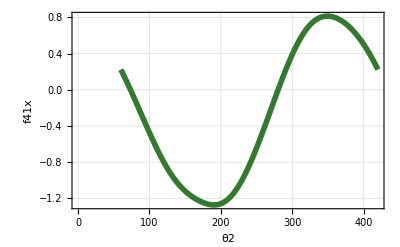

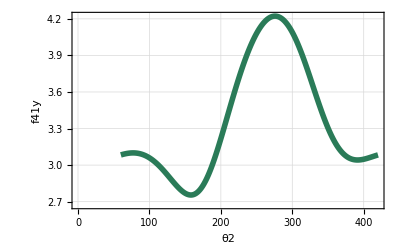

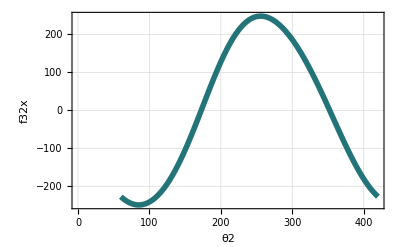

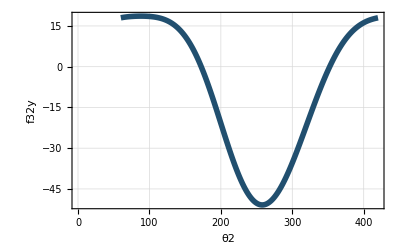

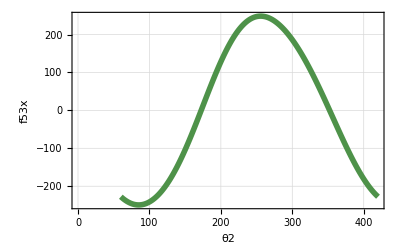

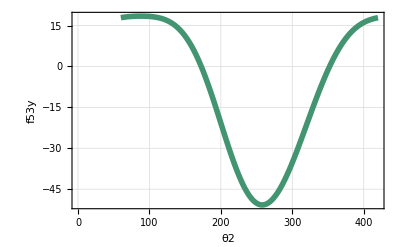

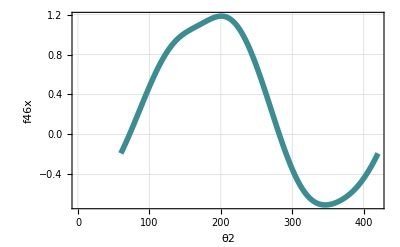

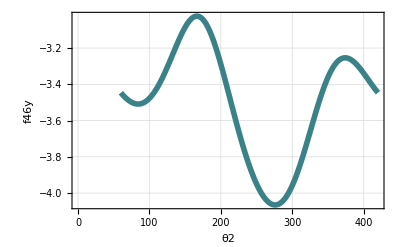

```mathematica
tablaAp=Table[{i,f41x}/.SolDin[i],{i,60,420,1}];
tablaBp=Table[{i,f41y}/.SolDin[i],{i,60,420,1}];
tablaCp=Table[{i,f32x}/.SolDin[i],{i,60,420,1}];
tablaDp=Table[{i,f32y}/.SolDin[i],{i,60,420,1}];
tablaEp=Table[{i,f53x}/.SolDin[i],{i,60,420,1}];
tablaFp=Table[{i,f53y}/.SolDin[i],{i,60,420,1}];
tablaGp=Table[{i,f46x}/.SolDin[i],{i,60,420,1}];
tablaHp=Table[{i,f46y}/.SolDin[i],{i,60,420,1}];
tablaIp=Table[{i,f56x}/.SolDin[i],{i,60,420,1}];
tablaJp=Table[{i,f56y}/.SolDin[i],{i,60,420,1}];
tablaKp=Table[{i,f01x}/.SolDin[i],{i,60,420,1}];
tablaLp=Table[{i,f01y}/.SolDin[i],{i,60,420,1}];
tablaMp=Table[{i,f05x}/.SolDin[i],{i,60,420,1}];
tablaNp=Table[{i,f05y}/.SolDin[i],{i,60,420,1}];
tablaOp=Table[{i,t01z}/.SolDin[i],{i,60,420,1}];

ListPlot[tablaAp,  Frame->True,  FrameLabel->{"θ2","f41x"},   Joined->True,      PlotStyle->{RGBColor[0.2078,0.4745,0.1882],Thickness[.01]},    GridLines->Automatic,    ImageSize->400]

ListPlot[tablaBp,  Frame->True,  FrameLabel->{"θ2","f41y"},  Joined->True,  PlotStyle->{RGBColor[0.1647,0.4823,0.345],Thickness[.01]},  GridLines->Automatic,  ImageSize->400]

ListPlot[tablaCp,  Frame->True,  FrameLabel->{"θ2","f32x"},  Joined->True,  PlotStyle->{RGBColor[0.1372,0.4549,0.4705],Thickness[.01]},  GridLines->Automatic,  ImageSize->400]

ListPlot[tablaDp,  Frame->True,  FrameLabel->{"θ2","f32y"},  Joined->True,  PlotStyle->{RGBColor[0.1294,0.3098,0.4352],Thickness[.01]},  GridLines->Automatic,  ImageSize->400]

ListPlot[tablaEp,  Frame->True,  FrameLabel->{"θ2","f53x"},   Joined->True,      PlotStyle->{RGBColor[0.3078,0.5745,0.2882],Thickness[.01]},    GridLines->Automatic,    ImageSize->400]

ListPlot[tablaFp,  Frame->True,  FrameLabel->{"θ2","f53y"},  Joined->True,  PlotStyle->{RGBColor[0.2647,0.5823,0.445],Thickness[.01]},  GridLines->Automatic,  ImageSize->400]

ListPlot[tablaGp,  Frame->True,  FrameLabel->{"θ2","f46x"},  Joined->True,  PlotStyle->{RGBColor[0.2372,0.5549,0.5705],Thickness[.01]},  GridLines->Automatic,  ImageSize->400]

ListPlot[tablaHp,  Frame->True,  FrameLabel->{"θ2","f46y"},  Joined->True,  PlotStyle->{RGBColor[0.2294,0.5098,0.5352],Thickness[.01]},  GridLines->Automatic,  ImageSize->400]
ListPlot[tablaIp,  Frame->True,  FrameLabel->{"θ2","f56x"},   Joined->True,      PlotStyle->{RGBColor[0.4078,0.6745,0.3882],Thickness[.01]},    GridLines->Automatic,    ImageSize->400]

ListPlot[tablaJp,  Frame->True,  FrameLabel->{"θ2","f56y"},  Joined->True,  PlotStyle->{RGBColor[0.3647,0.6823,0.545],Thickness[.01]},  GridLines->Automatic,  ImageSize->400]

ListPlot[tablaKp,  Frame->True,  FrameLabel->{"θ2","f01x"},  Joined->True,  PlotStyle->{RGBColor[0.3372,0.6549,0.6705],Thickness[.01]},  GridLines->Automatic,  ImageSize->400]

ListPlot[tablaLp,  Frame->True,  FrameLabel->{"θ2","f01y"},  Joined->True,  PlotStyle->{RGBColor[0.3294,0.5098,0.6352],Thickness[.01]},  GridLines->Automatic,  ImageSize->400]
ListPlot[tablaMp,  Frame->True,  FrameLabel->{"θ2","f05x"},   Joined->True,      PlotStyle->{RGBColor[0.5078,0.7745,0.4882],Thickness[.01]},    GridLines->Automatic,    ImageSize->400]

ListPlot[tablaNp,  Frame->True,  FrameLabel->{"θ2","f05y"},  Joined->True,  PlotStyle->{RGBColor[0.4647,0.7823,0.645],Thickness[.01]},  GridLines->Automatic,  ImageSize->400]

ListPlot[tablaOp,  Frame->True,  FrameLabel->{"θ2","t01z"},  Joined->True,  PlotStyle->{RGBColor[0.4372,0.7549,0.7705],Thickness[.01]},  GridLines->Automatic,  ImageSize->400]
```

### Gráficas de Normas de las fuerzas de reacción

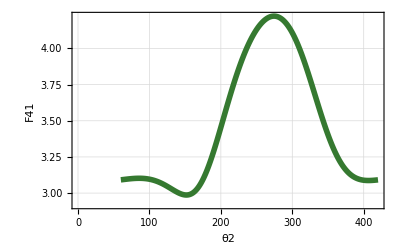

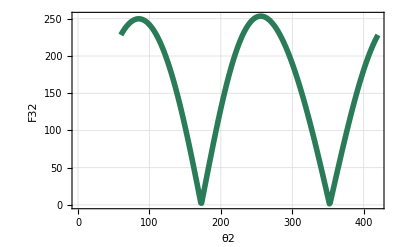

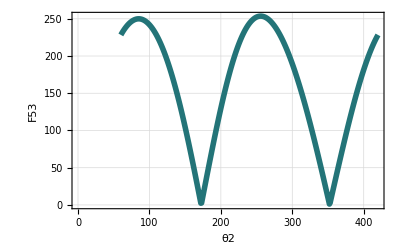

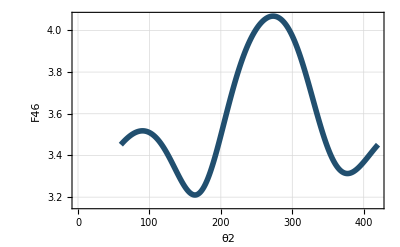

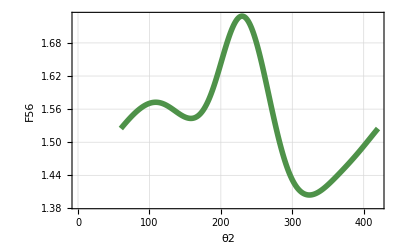

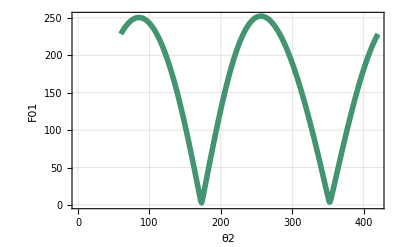

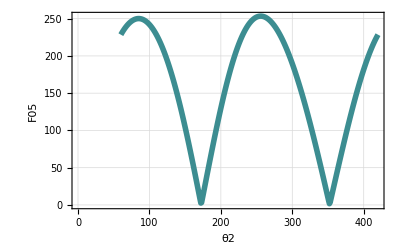

```mathematica
tablaPp=Table[{i,Norm[F41]}/.SolDin[i],{i,60,420,1}];
tablaQp=Table[{i,Norm[F32]}/.SolDin[i],{i,60,420,1}];
tablaRp=Table[{i,Norm[F53]}/.SolDin[i],{i,60,420,1}];
tablaSp=Table[{i,Norm[F46]}/.SolDin[i],{i,60,420,1}];
tablaTp=Table[{i,Norm[F56]}/.SolDin[i],{i,60,420,1}];
tablaUp=Table[{i,Norm[F01]}/.SolDin[i],{i,60,420,1}];
tablaVp=Table[{i,Norm[F05]}/.SolDin[i],{i,60,420,1}];


ListPlot[tablaPp,  Frame->True,  FrameLabel->{"θ2","F41"},   Joined->True,      PlotStyle->{RGBColor[0.2078,0.4745,0.1882],Thickness[.01]},    GridLines->Automatic,    ImageSize->400]

ListPlot[tablaQp,  Frame->True,  FrameLabel->{"θ2","F32"},  Joined->True,  PlotStyle->{RGBColor[0.1647,0.4823,0.345],Thickness[.01]},  GridLines->Automatic,  ImageSize->400]

ListPlot[tablaRp,  Frame->True,  FrameLabel->{"θ2","F53"},  Joined->True,  PlotStyle->{RGBColor[0.1372,0.4549,0.4705],Thickness[.01]},  GridLines->Automatic,  ImageSize->400]

ListPlot[tablaSp,  Frame->True,  FrameLabel->{"θ2","F46"},  Joined->True,  PlotStyle->{RGBColor[0.1294,0.3098,0.4352],Thickness[.01]},  GridLines->Automatic,  ImageSize->400]

ListPlot[tablaTp,  Frame->True,  FrameLabel->{"θ2","F56"},   Joined->True,      PlotStyle->{RGBColor[0.3078,0.5745,0.2882],Thickness[.01]},    GridLines->Automatic,    ImageSize->400]

ListPlot[tablaUp,  Frame->True,  FrameLabel->{"θ2","F01"},  Joined->True,  PlotStyle->{RGBColor[0.2647,0.5823,0.445],Thickness[.01]},  GridLines->Automatic,  ImageSize->400]

ListPlot[tablaVp,  Frame->True,  FrameLabel->{"θ2","F05"},  Joined->True,  PlotStyle->{RGBColor[0.2372,0.5549,0.5705],Thickness[.01]},  GridLines->Automatic,  ImageSize->400]
```

## Dinámica Trabajo Virtual

## Ecuación Dinámica

```mathematica
Clear[θ2,θ3,θ4,θ5,θ6];
Clear[ω2,ω3,ω4,ω5,ω6];
Clear[α2,α3,α4,α5,α6];
```

```mathematica
Fp=5*{Cos[270*Degree],Sin[270*Degree],0};

T01={0,0,t01z};
 T05=-{0,0,ω5};

EcDin  =+Fp.Vp+ T05.omega5 +T01.omega2 - m12*Ag12.Vg12-m3*Ag3.Vg3-m4*Ag4.Vg4-m5*Ag5.Vg5- m6*Ag6.Vg6- Ig12*alfa2.omega2-Ig3*alfa3.omega3-Ig4*alfa4.omega4-Ig5*alfa5.omega5-Ig6*alfa6.omega6;
```

## Solución Dinámica

```mathematica
ω2 = 50;
α2 =0;

For[i = 60, i ≤ 420,i+=1,
θ2=i*Degree;
SolDin[i]=Solve[
EcDin==0/.SolPos[i]/.SolVel[i]/.SolAcel[i],
t01z]//Flatten;
]
??SolDin;
```

Missing[UnknownSymbol,SolDin;]

## Gráfica de Par

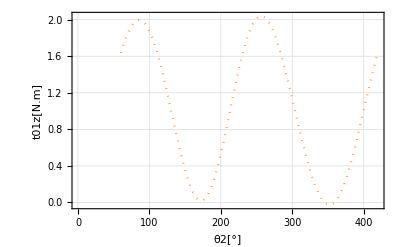

```mathematica
tablaUpp=Table[{i,(t01z/.SolDin[i])},{i,60,420,1}];

ListPlot[tablaUpp,
Frame->True,
FrameLabel->{"θ2[°]","t01z[N.m]"},
Joined->True,
PlotStyle->{{Orange,Dotted}},
GridLines->Automatic,
ImageSize->400]
```

## Comparación de Par de Torsión y fuerzas obtenidos por Newton

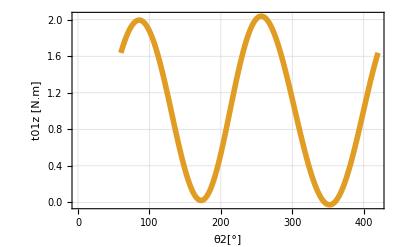

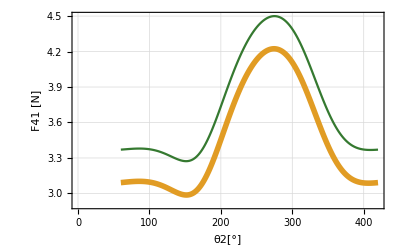

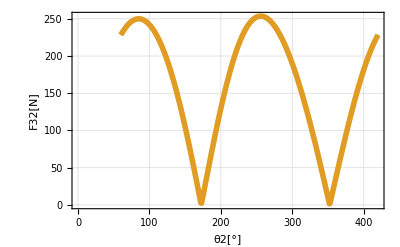

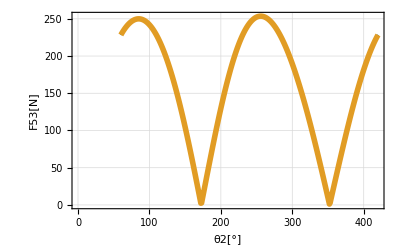

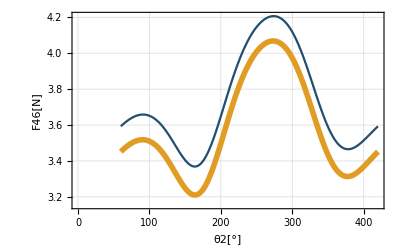

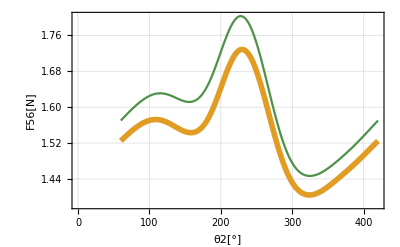

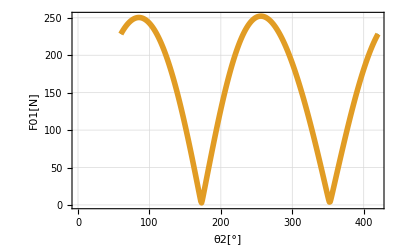

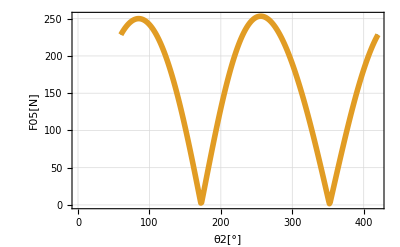

```mathematica
ListPlot[{tablaO,tablaOp},  Frame->True,  FrameLabel->{"θ2[°]","t01z [N.m]"},  Joined->True,  PlotStyle->{RGBColor[0.4372,0.7549,0.7705],Thickness[.01]},  GridLines->Automatic,  ImageSize->400]

ListPlot[{tablaP,tablaPp},  Frame->True,  FrameLabel->{"θ2[°]","F41 [N]"},   Joined->True,      PlotStyle->{RGBColor[0.2078,0.4745,0.1882],Thickness[.01]},    GridLines->Automatic,    ImageSize->400]

ListPlot[{tablaQ,tablaQp},  Frame->True,  FrameLabel->{"θ2[°]","F32[N]"},  Joined->True,  PlotStyle->{RGBColor[0.1647,0.4823,0.345],Thickness[.01]},  GridLines->Automatic,  ImageSize->400]

ListPlot[{ tablaR, tablaRp},  Frame->True,  FrameLabel->{"θ2[°]","F53[N]"},  Joined->True,  PlotStyle->{RGBColor[0.1372,0.4549,0.4705],Thickness[.01]},  GridLines->Automatic,  ImageSize->400]

ListPlot[{tablaS, tablaSp},  Frame->True,  FrameLabel->{"θ2[°]","F46[N]"},  Joined->True,  PlotStyle->{RGBColor[0.1294,0.3098,0.4352],Thickness[.01]},  GridLines->Automatic,  ImageSize->400]

ListPlot[{tablaT ,tablaTp},  Frame->True,  FrameLabel->{"θ2[°]","F56[N]"},   Joined->True,      PlotStyle->{RGBColor[0.3078,0.5745,0.2882],Thickness[.01]},    GridLines->Automatic,    ImageSize->400]

ListPlot[{tablaU ,tablaUp},  Frame->True,  FrameLabel->{"θ2[°]","F01[N]"},  Joined->True,  PlotStyle->{RGBColor[0.2647,0.5823,0.445],Thickness[.01]},  GridLines->Automatic,  ImageSize->400]

ListPlot[{tablaV ,tablaVp},  Frame->True,  FrameLabel->{"θ2[°]","F05[N]"},  Joined->True,  PlotStyle->{RGBColor[0.2372,0.5549,0.5705],Thickness[.01]},  GridLines->Automatic,  ImageSize->400]
```

## Comparación de Par de Torsión obtenido por los tres análisis

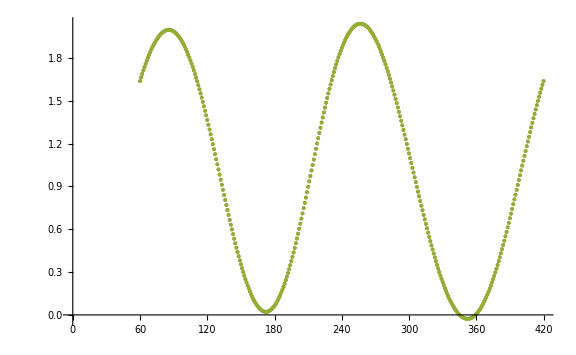

```mathematica
ListPlot[{tablaUpp,tablaOp, tablaO},

ImageSize->Large]
```